```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=20;
Ly=20;
A=Lx*Ly;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2,sx2dp[1+k Lx,(k+1)Lx]=I/2},{k,0,Ly-1}]

SX2DP=Table[sx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2,cx2dp[1+k Lx,(1+k)Lx]=1/2},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHI]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianQAHI[t_,t0_,m_,α_]:=t*(KroneckerProduct[SX2D+α*SX2DP,σ1]+KroneckerProduct[SY2D+α*SY2DP, σ2])+KroneckerProduct[-m*Cons+t0*(CX2D+CY2D+α*CX2DP+α*CY2DP),σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(* Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange] *)
```

```mathematica
(* {val,vec}=Eigensystem[HamiltonianQAHI[1.0,1.0,1.0,1.0]];  *)
```

```mathematica
(* ValVecAHI=SortBy[Transpose[{val,vec}],First];  *)
```

```mathematica
(* ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];  *)
```

```mathematica
(* ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];  *)
```

```mathematica
(* Show[ListPlot[ValAHI,Frame-> True,Axes-> False,PlotRange-> {{0,2A},{Min[ValAHIRange],Max[ValAHIRange]}}],Plot[0,{x,0,2A},PlotStyle-> Red],BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]  *)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*----------- Computation of Bott Index of the whole system -----------------*)
```

```mathematica
(* Clear[vecNormalized,ValVecNor,U,Ux,Vy,U,V,P,LogEigenValuesBott,Bott,BottIndex]  *)
```

```mathematica
(* vecNormalized=Table[Normalize[vec[[i]]],{i,1,2 A}];  *)
```

```mathematica
(* ValVecNor=SortBy[Transpose[{val,vecNormalized}],First]; *)
```

```mathematica
(* FilledEigenvectors=Table[ValVecNor[[i]][[2]], {i,1,A}];  *)
```

```mathematica
(* Clear[P]
P=Table[0,{i,1,2A},{j,1,2A}];  *)
```

```mathematica
(* Do[P+=TensorProduct[FilledEigenvectors[[i]] ,Conjugate[ FilledEigenvectors[[i]]]],{i, 1, A}];  *)
```

```mathematica
(* XList = Flatten[Transpose[Table[i,{i,1,Lx},{j,1,Ly}]]];  *)
```

```mathematica
(* YList = Flatten[Transpose[Table[j,{i,1,Lx},{j,1,Ly}]]];  *)
```

```mathematica
(* XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];  *)
```

```mathematica
(* YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];  *)
```

```mathematica
(* Ux =DiagonalMatrix[ Exp[2 π I XListKron /Lx]];  *)
```

```mathematica
(* Vy = DiagonalMatrix[Exp[2 π I YListKron/Ly]];  *)
```

```mathematica
(* U = P . Ux. P + IdentityMatrix[2 A] - P;  *)
```

```mathematica
(* V = P . Vy . P + IdentityMatrix[2A] - P;  *)
```

```mathematica
(* Bott = U.V.ConjugateTranspose[U].ConjugateTranspose[V];  *)
```

```mathematica
(* LogEigenValuesBott=Log[Eigenvalues[Bott]];  *)
```

```mathematica
(* BottIndex = Re[(I/(2π))Total[LogEigenValuesBott]]  *)
```

```mathematica
(**----Clear memory for quasicrystal----**)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------------quasicrystal--------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

800

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+20
LineDn[x_]:=((1+√5)/2)^-1*(x-2)-6
```

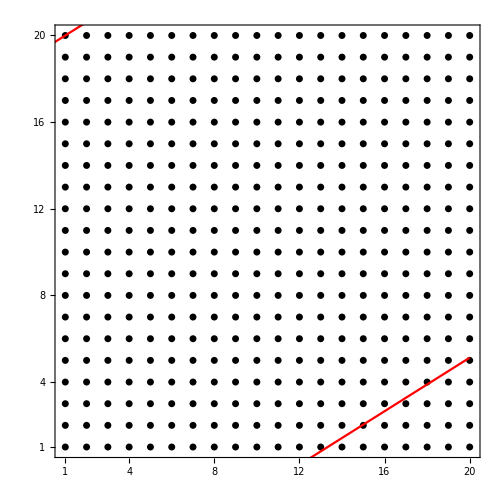

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron, Ux, Vy, P,U,V,LogEigenValuesBott,Bott, BottIndexQuasi]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonup=Sort[FibonupNew]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,21,22,23,24,25,26,27,28,29,30,31,32,33,34,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400}

```mathematica
(** Fibonup2={}; **)
```

```mathematica
(** Do[Do[Fibonup2=Append[Fibonup2,x+(y-1)*Lx],{y,6,15}],{x,6,15}]**)
```

```mathematica
(** Fibonup2**)
```

{106,126,146,166,186,206,226,246,266,286,107,127,147,167,187,207,227,247,267,287,108,128,148,168,188,208,228,248,268,288,109,129,149,169,189,209,229,249,269,289,110,130,150,170,190,210,230,250,270,290,111,131,151,171,191,211,231,251,271,291,112,132,152,172,192,212,232,252,272,292,113,133,153,173,193,213,233,253,273,293,114,134,154,174,194,214,234,254,274,294,115,135,155,175,195,215,235,255,275,295}

```mathematica
(** Clear[Fibonup]**)
```

```mathematica
(** Fibonup = Fibonup2**)
```

{106,126,146,166,186,206,226,246,266,286,107,127,147,167,187,207,227,247,267,287,108,128,148,168,188,208,228,248,268,288,109,129,149,169,189,209,229,249,269,289,110,130,150,170,190,210,230,250,270,290,111,131,151,171,191,211,231,251,271,291,112,132,152,172,192,212,232,252,272,292,113,133,153,173,193,213,233,253,273,293,114,134,154,174,194,214,234,254,274,294,115,135,155,175,195,215,235,255,275,295}

```mathematica
YList = Ceiling[Fibonup/Lx]
```

{6,7,8,9,10,11,12,13,14,15,6,7,8,9,10,11,12,13,14,15,6,7,8,9,10,11,12,13,14,15,6,7,8,9,10,11,12,13,14,15,6,7,8,9,10,11,12,13,14,15,6,7,8,9,10,11,12,13,14,15,6,7,8,9,10,11,12,13,14,15,6,7,8,9,10,11,12,13,14,15,6,7,8,9,10,11,12,13,14,15,6,7,8,9,10,11,12,13,14,15}

```mathematica
XList = Fibonup - (YList - 1)Lx
```

{6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15}

```mathematica
(**Check that the list is correct**)
```

```mathematica
XList + (YList-1)*Lx - Fibonup
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
Ux =DiagonalMatrix[ Exp[2 π I XListKron /Lx]];
```

```mathematica
Vy = DiagonalMatrix[Exp[2 π I YListKron/Ly]];
```

```mathematica
(**--Compare with the previous (manually calculated) Fibonup for 20x20 sites--**)
```

```mathematica
(**--Fibonup={1,22,23,43,44,45,65,66,86,87,88,108,109,110,130,131,151,152,153,173,174,194,195,196,216,217,218,238,239,259,260};--**)
```

```mathematica
Fibondown=Table[Fibonup[[j]]+A,{j,1,Dimensions[Fibonup][[1]]}];
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

200

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

600

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
a=F1;
Do[
a=Drop[a,{TotalFibon[[NOrbitalsQuasi-i]]}],
{i,0,NOrbitalsQuasi-1,1}
]
```

```mathematica
Dimensions[a]
```

{600}

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
HTrial=HamiltonianQAHI[1.,1.,1.5,1.0];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
Hfbfb[i_Integer,j_Integer]=0;
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
]
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
H2d2d[i_Integer,j_Integer]=0;
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
]
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}];
```

```mathematica
(*------------------------------------------------------*)
```

```mathematica
H2dfb[i_Integer,j_Integer]=0;

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
]
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*-------------------------------------------------*)
```

```mathematica
Hfb2d[i_Integer,j_Integer]=0;

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
]
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}];
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon,OnlyEigenvalue]
```

```mathematica
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB);
```

```mathematica
(**------Check that HFibonRenor is Hermitian------**)
```

```mathematica
(**--- ConjugateTranspose[HFibonRenor] - HFibonRenor//Chop ---**)
```

```mathematica
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor];
```

```mathematica
ValVecFibon=SortBy[Transpose[{ValueFibon,VecFibon}],First];
```

```mathematica
ValFibon=Table[{j,ValVecFibon[[j,1]]},{j,1,NOrbitalsQuasi}]//Chop;
```

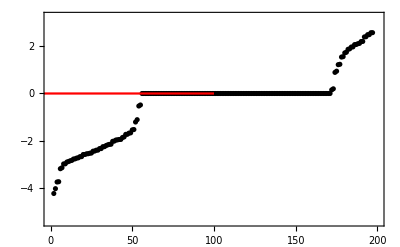

```mathematica
Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black],Plot[0,{x,-100,100},PlotStyle-> Red]]
```

```mathematica
OnlyEigenvalue=Table[ValFibon[[j,2]],{j,1,NOrbitalsQuasi}];
```

```mathematica
Tr[OnlyEigenvalue]//Chop
```

34.1235

```mathematica
(**---- Calculation of Bott Index of the quasicrystal ----**)
```

```mathematica
FilledEigenvectors=Table[ValVecFibon[[i]][[2]], {i,1,NOrbitalsQuasi/2}];
```

```mathematica
(** We create a projector P on the space of filled eigenstates **)
```

```mathematica
P = Table[0,{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}];
```

```mathematica
Do[P+=TensorProduct[FilledEigenvectors[[i]] ,Conjugate[ FilledEigenvectors[[i]]]],{i, 1, NOrbitalsQuasi/2}];
```

```mathematica
Dimensions[P]
```

{200,200}

```mathematica
U = P . Ux . P + IdentityMatrix[NOrbitalsQuasi] - P;
```

```mathematica
V = P . Vy . P + IdentityMatrix[NOrbitalsQuasi] - P;
```

```mathematica
(** To save computer from hanging, we clear some memory **)
```

```mathematica
Clear[ Bott, LogEigenValuesBott, BottIndexQuasi]
```

```mathematica
Bott = U.V.ConjugateTranspose[U].ConjugateTranspose[V];
```

```mathematica
Clear[P,U,V, Ux, Vy]
```

```mathematica
LogEigenValuesBott=Log[Eigenvalues[Bott]];
```

Bott index of quasicrystal

```mathematica
BottIndexQuasi = Re[(I/(2π))Total[LogEigenValuesBott]]
```

2.85117×10^-6

```mathematica
percentageOfOrbitalsInside = N[NOrbitalsQuasi/(2*A)]
```

0.25

```mathematica
NSitesInside = NOrbitalsQuasi/2
```

100

```mathematica
(*---------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*---------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[τ,ν,x,Fibon1D,largestX]
```

```mathematica
τ=1/D[LineUp[x],x];
ν=√(1+τ^2);
```

```mathematica
x[m_]:=m/ν+1/(τ*ν)*Round[m/τ]
```

```mathematica
Fibon1D=Table[{1+N[x[m]],0},{m,0,NOrbitalsQuasi/2}];
```

```mathematica
largestX=Ceiling[Fibon1D[[Dimensions[Fibon1D][[1]],1]]]
```

74

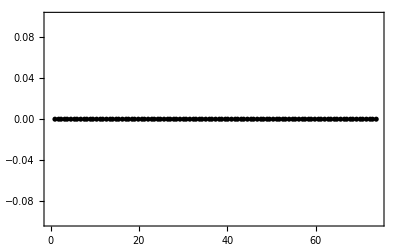

```mathematica
ListPlot[Fibon1D,Frame-> True,Axes-> False,PlotRange->{{0,largestX},{-0.1,0.1}},PlotStyle-> Black]
```

```mathematica
Fibon1D[[3,1]]
```

2.37638

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
ValFibon[[(NOrbitalsQuasi/2)+1,2]]
```

0

```mathematica
Clear[J,TabDataFibon,TDFibon,TabFibonacci]
```

```mathematica
J=NOrbitalsQuasi/2;
```

```mathematica
TabDataFibon=Table[{Fibon1D[[i,1]],0,
Abs[ValVecFibon[[J,2,i]]]^2+Abs[ValVecFibon[[J,2,i+NOrbitalsQuasi/2]]]^2

+Abs[ValVecFibon[[J+1,2,i]]]^2+Abs[ValVecFibon[[J+1,2,i+NOrbitalsQuasi/2]]]^2

},{i,1,NOrbitalsQuasi/2}];
```

```mathematica
TDFibon=Flatten[TabDataFibon];
```

```mathematica
TabFibonacci=Table[{TDFibon[[i]],TDFibon[[i+1]],TDFibon[[i+2]]},{i,1,3*NOrbitalsQuasi/2,3}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[colorfunc,rng,P1]
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
rng={0,Max[#]}&@TabFibonacci[[All,3]];
```

```mathematica
rng[[2]]
```

0.123602

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 12},Ticks-> {{0,"0.00"},{rng[[2]]/2,"0.30"},{rng[[2]]-10^-3,"0.60"}}]
```

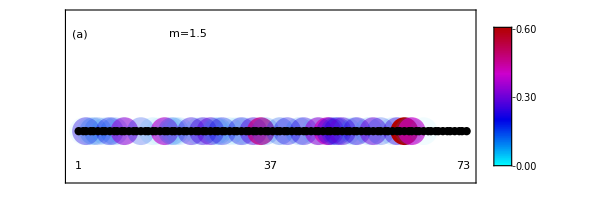

```mathematica
Show[Graphics[{PointSize[0.05],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibonacci,
Frame->True,FrameTicks-> {None,None},FrameStyle-> Black,
BaseStyle-> 18,
PlotRange-> {{0.0,largestX},{-3.5,8.5}}],
ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.015]}]
,
Epilog-> {Inset[1,{1,-2.5}],Inset[Ceiling[largestX/2],{Ceiling[largestX/2],-2.5}],Inset[largestX-1,{largestX-1,-2.5}],
Rotate[Inset[P1,{10.5,5.00}],90 Degree],Inset["m=1.5",{21.5,7}],
Inset["(a)",{1.25,7}]
}
]
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

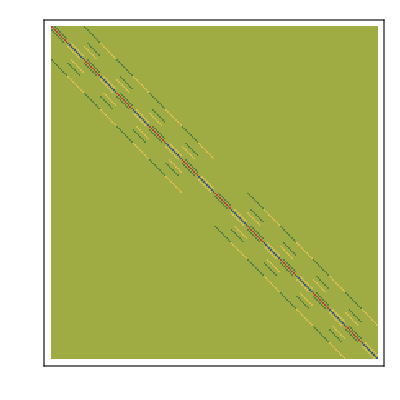

```mathematica
ArrayPlot[Re[HFBFB[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```

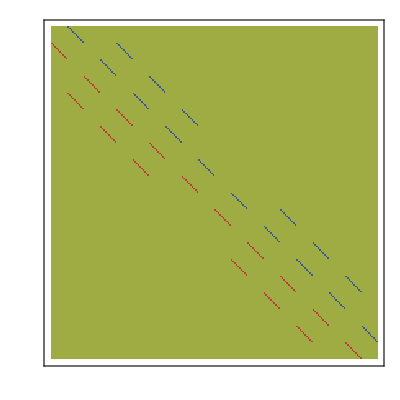

```mathematica
ArrayPlot[Im[HFBFB[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------------*)
```

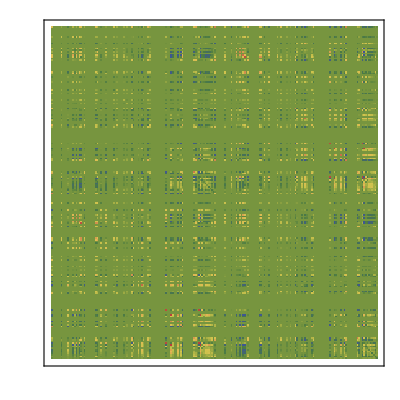

```mathematica
ArrayPlot[Re[HFibonRenor[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},ColorFunction->"DarkRainbow"]
```

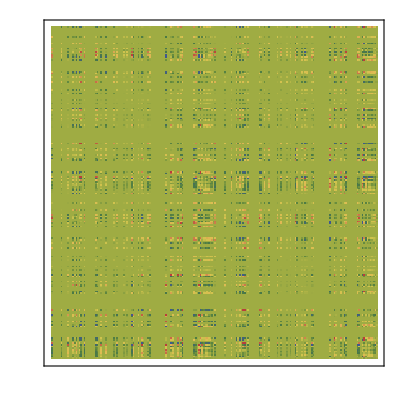

```mathematica
ArrayPlot[Im[HFibonRenor[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```